```mathematica
43^2/(2 246^2)//N
```

0.015277

0.68986

0.015277

74.2503

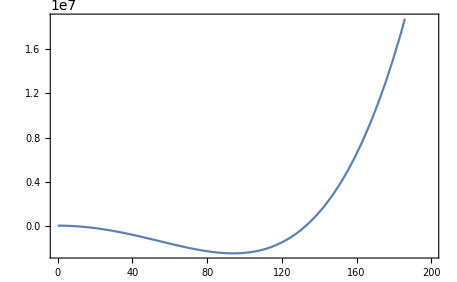

General::munfl: (1.81706×10^-25)^13 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.81706×10^-25)^14 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.81706×10^-25)^15 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

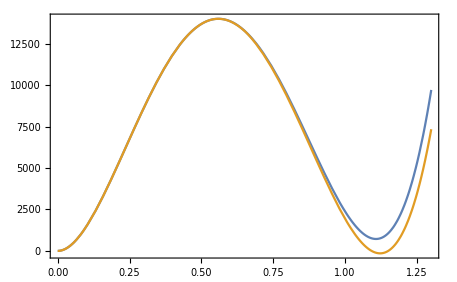

General::munfl: (1.68509×10^-25)^13 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.68509×10^-25)^14 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.68509×10^-25)^15 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

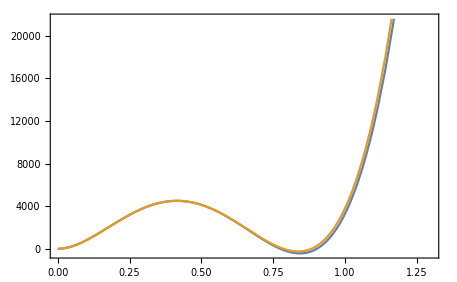

```mathematica
v0=246;
gSM=0.65;
gYSM=0.36;
ytSM=120/v0 √2//N
mWSM=1/4 gSM^2 v0^2;
mZSM=1/4(gSM^2+gYSM^2)v0^2;
mtSM=1/2 ytSM^2 v0^2;
aB=Exp[3.91];
aF=Exp[1.14];
BSM=3/(64 π^2 v0^4)(2 mWSM^2+mZSM^2-4 mtSM^2);
DSM=1/(8 v0^2)(2mWSM+mZSM+2mtSM);
ESM=1/(4π v0^3)(2 mWSM^(3/2)+mZSM^(3/2));
mH=43;
λSM=(mH/(√2 v0))^2//N
T0SM=√(1/(4DSM)(mH^2-8BSM v0^2))
mgauge=({{gSM^2 x1^2/4+11/6 gSM^2 x2^2, -gSM gYSM x1^2/4}, {-gSM gYSM x1^2/4, gYSM^2 x1^2/4+11/6 gYSM^2 x2^2}});
λTSM[T_]:=λSM-3/(16 π^2 v0^4)(2 mWSM^2 Log[mWSM/(aB T^2)]+mZSM^2 Log[mZSM/(aB T^2)]-4 mtSM^2 Log[mtSM/(aF T^2)]);
V0[ϕ_]:=-1/2 λSM v0^2 ϕ^2+λSM/4 ϕ^4+2BSM v0^2 ϕ^2-3/2 BSM ϕ^4+BSM ϕ^4 Log[ϕ^2/v0^2];
VFTSM[ϕ_,T_]:=T^4/(2 π^2)(6JBfit[(mWSM ϕ^2)/(T^2 v0^2)]+3JBfit[(mZSM ϕ^2)/(T^2 v0^2)]-12JFfit[(mtSM ϕ^2)/(T^2 v0^2)]);
VSM[ϕ_,T_]:=DSM(T^2-T0SM^2)ϕ^2-ESM T ϕ^3+λTSM[T]/4 ϕ^4;
gaugeL=Eigenvalues[mgauge]//FullSimplify;
mWL[ϕ_,T_]:=1/4 gtest^2 ϕ^2+11/6 gtest^2 T^2;(*longitudal mode for W+ and W-, or W1 and W2*)
mBL[ϕ_,T_]:=gaugeL[[1]]/.{x1->ϕ,x2->T};(*SM B particle, massless*)
mZL[ϕ_,T_]:=gaugeL[[2]]/.{x1->ϕ,x2->T};(*Zprime particle*)
resum[ϕ_,T_]:=T/(12π)(2((mWSM ϕ^2/v0^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZSM ϕ^2/v0^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
VSMfull[ϕ_,T_]:=V0[ϕ]+VFTSM[ϕ,T]-VFTSM[10^-10,T]
VSMfullresum[ϕ_,T_]:=V0[ϕ]+VFTSM[ϕ,T]-VFTSM[10^-10,T]+resum[ϕ,T]-resum[10^-10,T];
VhighTresum[ϕ_,T_]:=DSM(T^2-T0SM^2)ϕ^2-ESM T ϕ^3+λTSM[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
Plot[VSM[ϕ,10^-5],{ϕ,0,200}]
Tplot=0.9402T0;
Plot[{VSM[0.963Tplot*ratio,0.963Tplot],VSMfull[0.963Tplot*ratio,0.963Tplot]},{ratio,0,1.3}]
Plot[{VSMfullresum[Tplot*ratio,Tplot],VhighTresum[Tplot*ratio,Tplot]},{ratio,0,1.3}]
```